# The simple sigmoid (logistic function)

## Derivatives as a function of z

```mathematica
σ[z_]:=1/(1+ⅇ^-z)
```

```mathematica
D[σ[z], z]
```

ⅇ^-z/((1+ⅇ^-z)^2)

```mathematica
σ1[z_]:=ⅇ^-z/((1+ⅇ^-z)^2)
```

```mathematica
D[σ[z], z,z]
```

(2 ⅇ^(-2 z))/((1+ⅇ^-z)^3)-ⅇ^-z/((1+ⅇ^-z)^2)

```mathematica
σ2[z_]:=(2 ⅇ^(-2 z))/((1+ⅇ^-z)^3)-ⅇ^-z/((1+ⅇ^-z)^2)
```

```mathematica
D[σ[z], z,z,z]
```

(6 ⅇ^(-3 z))/((1+ⅇ^-z)^4)-(6 ⅇ^(-2 z))/((1+ⅇ^-z)^3)+ⅇ^-z/((1+ⅇ^-z)^2)

```mathematica
σ3[z_]:=(6 ⅇ^(-3 z))/((1+ⅇ^-z)^4)-(6 ⅇ^(-2 z))/((1+ⅇ^-z)^3)+ⅇ^-z/((1+ⅇ^-z)^2)
```

```mathematica
D[σ[z], z,z,z,z]
```

(24 ⅇ^(-4 z))/((1+ⅇ^-z)^5)-(36 ⅇ^(-3 z))/((1+ⅇ^-z)^4)+(14 ⅇ^(-2 z))/((1+ⅇ^-z)^3)-ⅇ^-z/((1+ⅇ^-z)^2)

```mathematica
σ4[z_]:=(24 ⅇ^(-4 z))/((1+ⅇ^-z)^5)-(36 ⅇ^(-3 z))/((1+ⅇ^-z)^4)+(14 ⅇ^(-2 z))/((1+ⅇ^-z)^3)-ⅇ^-z/((1+ⅇ^-z)^2)
```

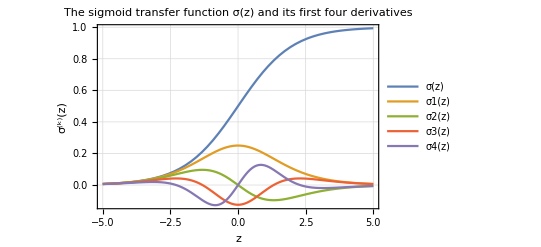

```mathematica
Plot[{σ[z],σ1[z],σ2[z],σ3[z],σ4[z]},{z,-5,5},PlotRange->Full,AxesLabel->{"z","σ^(k)(z)"},PlotLegends->"Expressions",PlotLabel->"The sigmoid transfer function σ(z) and its first four derivatives", Frame->True,GridLines->Automatic]
```

## Derivatives as a function of σ

```mathematica
s1[s_]:=s-s^2
```

```mathematica
s2[s_]:=2 s^3-3 s^2+s
```

```mathematica
s3[s_]:=-6 s^4+12 s^3-7 s^2+s
```

```mathematica
s4[s_]:=24 s^5-60 s^4+50 s^3-15 s^2+s
```

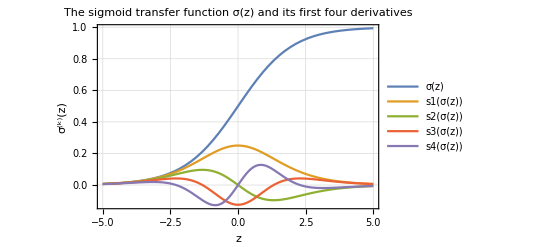

```mathematica
Plot[{σ[z],s1[σ[z]],s2[σ[z]],s3[σ[z]],s4[σ[z]]},{z,-5,5},PlotRange->Full,AxesLabel->{"z","σ^(k)(z)"},PlotLegends->"Expressions",PlotLabel->"The sigmoid transfer function σ(z) and its first four derivatives", Frame->True,GridLines->Automatic]
```

## Difference between methods

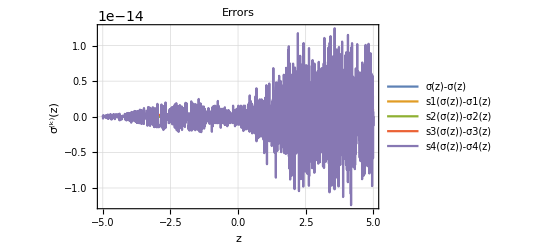

```mathematica
Plot[{σ[z]-σ[z],s1[σ[z]]-σ1[z],s2[σ[z]]-σ2[z],s3[σ[z]]-σ3[z],s4[σ[z]]-σ4[z]},{z,-5,5},PlotRange->Full,AxesLabel->{"z","σ^(k)(z)"},PlotLegends->"Expressions",PlotLabel->"Errors", Frame->True,GridLines->Automatic]
```

## Test cases for code in sigma.py

```mathematica
ztest=1
```

1

```mathematica
{σ[ztest],σ1[ztest],σ2[ztest],σ3[ztest],σ4[ztest]}//N
```

{0.731059,0.196612,-0.0908577,-0.0353256,0.123507}

```mathematica
{σ[ztest],s1[σ[ztest]],s2[σ[ztest]],s3[σ[ztest]],s4[σ[ztest]]}//N
```

{0.731059,0.196612,-0.0908577,-0.0353256,0.123507}